{{1,106.},{2,77.6},{3,51.1},{4,27.3},{5,3.2},{6,-20.7},{7,-42.9},{8,-62.7},{9,-81.}}

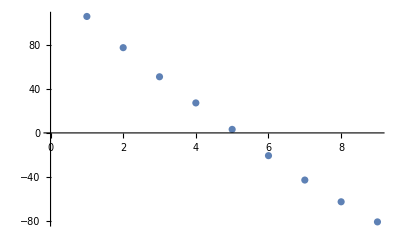

```mathematica
U1={106.0,77.6,51.1,27.3,3.2,-20.7,-42.9,-62.7,-81.0};
data1=Table[{i,U1[[i]]},{i,1,9}]
grp1=ListPlot[data1]
```

```mathematica
fd1=Fit[data1,{1,x},x]
```

123.508-23.415 x

```mathematica
Needs["LinearRegression`"]
Regress[data1,{1,x},x,RegressionReport->{RSquared}]
```

{RSquared→0.996442}

```mathematica
{RSquared->0.9987210685724566}
```

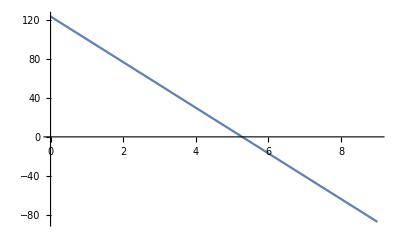

```mathematica
Plot[fd1,{x,0,9}]
```

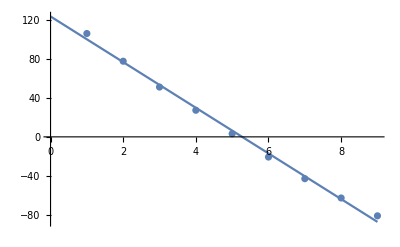

```mathematica
Show[%,grp1]
```

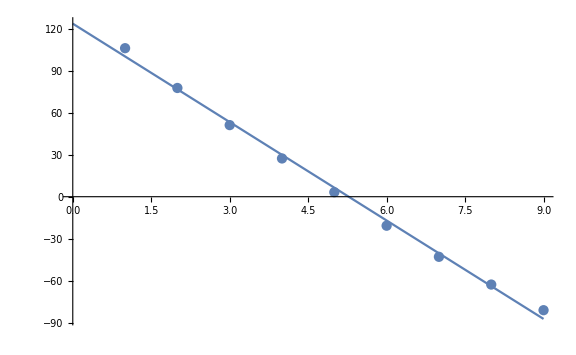

```mathematica
Show[%35,ImageSize->Large]
```

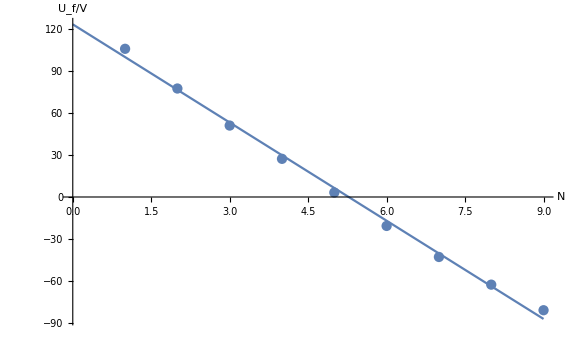

```mathematica
Show[%36,AxesLabel->{HoldForm[N],HoldForm[U_f/V]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```